True

{0.000909961,0.00438393,-0.000867167,0.00114055,-0.00104553,0.000489347,-0.000615812,0.000931747,0.000170407,-0.00168723,-0.00145683,-0.00187975,0.00276645,-0.00152978,-0.00104757,0.0012759,0.0068051,0.0000606508}

{-0.00122571,-0.00576884,0.00213636,-0.00596133,0.00230666,-0.000478133,0.00162665,0.000996034,-0.00230045,-0.00172148,-0.00240636,-0.00108177,-0.00294432,-0.000635886,-0.00714921,0.0000479285,-0.00267876,-0.000568892}

Vwap no error test for normality:

| Statistic | P-Value
Kolmogorov-Smirnov | 0.194269 | 0.077631

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is not rejected at the 5. percent level based on the Kolmogorov-Smirnov test.

Vwap error test for normality:

| Statistic | P-Value
Kolmogorov-Smirnov | 0.130294 | 0.588892

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is not rejected at the 5. percent level based on the Kolmogorov-Smirnov test.

True

| Statistic | P-Value
Mann-Whitney | 226. | 0.0445317

The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.

| Statistic | P-Value
T | 2.44395 | 0.0198691

The null hypothesis that the mean difference is 0 is rejected at the 5. percent level based on the T test.

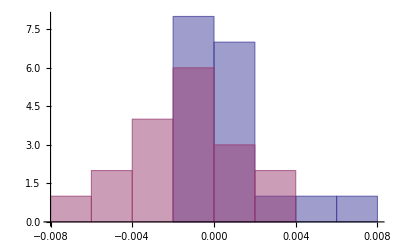

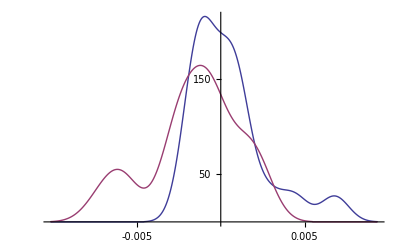

```mathematica
ClearAll[vwapnoerror, vwapnoerroraggressive, vwaperror,vwapnoerrordiff, vwaperrordiff];
(*vwapnoerror={
{100.002, 100.002}, 
{100.002, 100.001},
{100.000, 99.999},
{100.000,100.002},
{100.000, 100.001},
{100.004, 100.003},
{100.002, 100.001},
{100.002, 100.002},
{100.002, 100.001},
{100.000, 100.000},
{100.002, 100.001},
{100.003, 100.002}
};

vwaperror = {
{100.003, 100.004},
{100.001, 100.002},
{100.002, 100.003},
{100.002, 100.003},
{100.000, 100.001},
{100.002, 100.003},
{99.998, 99.999},
{100.001, 100.003},
{100.004, 100.005},
{100.001, 100.002},
{100.002, 100.003},
{100.003, 100.003}
};*)

vwapnoerroraggressive = {
{101.664, 101.285},
{105.01, 105.167},
{93.3488, 93.2235},
{101.705, 102.074},
{102.558, 102.321},
{100.09, 100.216},
{98.7107, 98.6845},
{98.3297, 98.6201},
{101.026, 101.139},
{100.131, 100.327},
{104.888, 104.813},
{96.2857, 95.9692},
{98.8096, 98.5212},
{99.9813, 99.6531},
{106.801, 106.815},
{97.6307,97.64},
{103.589, 103.594},
{101.399, 101.145}
};



vwapnoerror={
{106.598, 106.501},
{97.173, 96.747},
{95.714, 95.797},
{99.952, 99.838},
{97.558, 97.660},
{102.177, 102.127},
{100.680, 100.742},
{101.959, 101.864},
{99.761, 99.744},
{101.942, 102.114},
{99.531, 99.676},
{107.461, 107.663},
{92.176, 91.921},
{101.322, 101.477},
{93.550, 93.648},
{103.456, 103.324},
{103.158, 102.456},
{98.927, 98.921}
};

vwaperror = {
{104.429, 104.557},
{97.940, 98.505},
{98.298, 98.088},
{101.152, 101.755},
{104.480, 104.239},
{102.482, 102.531},
{105.124, 104.953},
{108.430, 108.322},
{99.111, 99.339},
{99.333, 99.504},
{101.398, 101.642},
{97.988, 98.094},
{100.193, 100.488},
{100.647, 100.711},
{102.389, 103.121},
{104.322, 104.317},
{102.286, 102.560},
{107.226, 107.287}
};

(*Length[vwapnoerror]==Length[vwaperror]*)
Length[vwapnoerror]==Length[vwapnoerroraggressive]

(*vwapnoerrordiff = #[[1]]-#[[2]]&/@vwapnoerror
vwaperrordiff = #[[1]]-#[[2]]&/@vwapnoerroraggressive
(*vwaperrordiff = #[[1]]-#[[2]]&/@vwaperror*)*)

(*vwapnoerrordiff = 1-#[[2]]/#[[1]]&/@vwapnoerror
vwaperrordiff = 1-#[[2]]/#[[1]]&/@vwaperror*)

vwapnoerrordiff = 1-#[[2]]/#[[1]]&/@vwapnoerror
vwaperrordiff = 1-#[[2]]/#[[1]]&/@vwaperror

Print["Vwap no error test for normality:"];
Print[KolmogorovSmirnovTest[vwapnoerrordiff ,Automatic,"TestDataTable"]];
Print[KolmogorovSmirnovTest[vwapnoerrordiff ,Automatic,"TestConclusion"]];

Print["Vwap error test for normality:"];
Print[KolmogorovSmirnovTest[vwaperrordiff ,Automatic,"TestDataTable"]];
Print[KolmogorovSmirnovTest[vwaperrordiff ,Automatic,"TestConclusion"]];

Length[vwapnoerrordiff]==Length[vwaperrordiff]


Print[MannWhitneyTest[{vwapnoerrordiff, vwaperrordiff},Automatic,"TestDataTable"]];
Print[MannWhitneyTest[{vwapnoerrordiff, vwaperrordiff},Automatic,"TestConclusion"]];

Print[TTest[{vwapnoerrordiff, vwaperrordiff},Automatic,"TestDataTable"]];
Print[TTest[{vwapnoerrordiff, vwaperrordiff},Automatic,"TestConclusion"]];

Histogram[{vwapnoerrordiff, vwaperrordiff}]
SmoothHistogram[{vwapnoerrordiff, vwaperrordiff}]
```